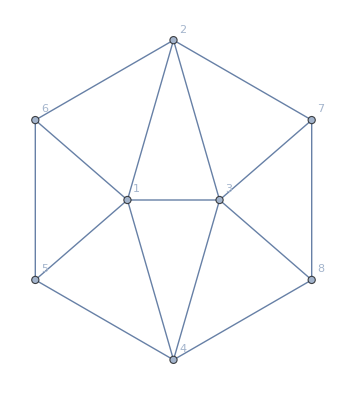

```mathematica
g=Graph[EdgeList[EdgeAdd[WheelGraph[6,VertexLabels->"Name"],{2 <->7,3 <->7,3 <->8,4 <->8,7 <->8}]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
Table[x->ChromaticPolynomial[g,x],{x,1,10}]
```

{1→0,2→0,3→0,4→312,5→8040,6→78120,7→454440,8→1916880,9→6480432,10→18632880}

```mathematica
ChromaticPolynomial[g,x]//CompleteBaseCoeff
```

{0,0,0,0,13,54,48,13,1}

```mathematica
Map[SymbolLevel[#[[1]]]->Map[SymbolToLabel,#]&,GatherBy[Sort[FindFullFormula[g],SymbolLevel[#1]<SymbolLevel[#2]&],SymbolLevel]]//Sort
```

{4→{17♁24♁35♁68,17♁24♁36♁58,17♁258♁36♁4,17♁258♁3♁46,17♁28♁35♁46,18♁24♁35♁67,18♁24♁36♁57,18♁25♁36♁47,18♁25♁3♁467,18♁2♁35♁467,1♁258♁36♁47,1♁258♁3♁467,1♁28♁35♁467},5→{17♁24♁35♁6♁8,17♁24♁36♁5♁8,17♁24♁3♁58♁6,17♁24♁3♁5♁68,17♁25♁36♁4♁8,17♁25♁3♁46♁8,17♁25♁3♁4♁68,17♁258♁3♁4♁6,17♁28♁35♁4♁6,17♁28♁36♁4♁5,17♁28♁3♁46♁5,17♁2♁35♁46♁8,17♁2♁35♁4♁68,17♁2♁36♁4♁58,17♁2♁3♁46♁58,18♁24♁35♁6♁7,18♁24♁36♁5♁7,18♁24♁3♁57♁6,18♁24♁3♁5♁67,18♁25♁36♁4♁7,18♁25♁3♁46♁7,18♁25♁3♁47♁6,18♁25♁3♁4♁67,18♁2♁35♁46♁7,18♁2♁35♁47♁6,18♁2♁35♁4♁67,18♁2♁36♁47♁5,18♁2♁36♁4♁57,18♁2♁3♁46♁57,18♁2♁3♁467♁5,1♁24♁35♁67♁8,1♁24♁35♁68♁7,1♁24♁36♁57♁8,1♁24♁36♁58♁7,1♁24♁3♁57♁68,1♁24♁3♁58♁67,1♁25♁36♁47♁8,1♁258♁36♁4♁7,1♁25♁3♁467♁8,1♁258♁3♁46♁7,1♁25♁3♁47♁68,1♁258♁3♁47♁6,1♁258♁3♁4♁67,1♁28♁35♁46♁7,1♁28♁35♁47♁6,1♁28♁35♁4♁67,1♁28♁36♁47♁5,1♁28♁36♁4♁57,1♁28♁3♁46♁57,1♁28♁3♁467♁5,1♁2♁35♁467♁8,1♁2♁35♁47♁68,1♁2♁36♁47♁58,1♁2♁3♁467♁58},6→{17♁24♁3♁5♁6♁8,17♁25♁3♁4♁6♁8,17♁28♁3♁4♁5♁6,17♁2♁35♁4♁6♁8,17♁2♁36♁4♁5♁8,17♁2♁3♁46♁5♁8,17♁2♁3♁4♁58♁6,17♁2♁3♁4♁5♁68,18♁24♁3♁5♁6♁7,18♁25♁3♁4♁6♁7,18♁2♁35♁4♁6♁7,18♁2♁36♁4♁5♁7,18♁2♁3♁46♁5♁7,18♁2♁3♁47♁5♁6,18♁2♁3♁4♁57♁6,18♁2♁3♁4♁5♁67,1♁24♁35♁6♁7♁8,1♁24♁36♁5♁7♁8,1♁24♁3♁57♁6♁8,1♁24♁3♁58♁6♁7,1♁24♁3♁5♁67♁8,1♁24♁3♁5♁68♁7,1♁25♁36♁4♁7♁8,1♁25♁3♁46♁7♁8,1♁25♁3♁47♁6♁8,1♁25♁3♁4♁67♁8,1♁25♁3♁4♁68♁7,1♁258♁3♁4♁6♁7,1♁28♁35♁4♁6♁7,1♁28♁36♁4♁5♁7,1♁28♁3♁46♁5♁7,1♁28♁3♁47♁5♁6,1♁28♁3♁4♁57♁6,1♁28♁3♁4♁5♁67,1♁2♁35♁46♁7♁8,1♁2♁35♁47♁6♁8,1♁2♁35♁4♁67♁8,1♁2♁35♁4♁68♁7,1♁2♁36♁47♁5♁8,1♁2♁36♁4♁57♁8,1♁2♁36♁4♁58♁7,1♁2♁3♁46♁57♁8,1♁2♁3♁46♁58♁7,1♁2♁3♁467♁5♁8,1♁2♁3♁47♁58♁6,1♁2♁3♁47♁5♁68,1♁2♁3♁4♁57♁68,1♁2♁3♁4♁58♁67},7→{17♁2♁3♁4♁5♁6♁8,18♁2♁3♁4♁5♁6♁7,1♁24♁3♁5♁6♁7♁8,1♁25♁3♁4♁6♁7♁8,1♁28♁3♁4♁5♁6♁7,1♁2♁35♁4♁6♁7♁8,1♁2♁36♁4♁5♁7♁8,1♁2♁3♁46♁5♁7♁8,1♁2♁3♁47♁5♁6♁8,1♁2♁3♁4♁57♁6♁8,1♁2♁3♁4♁58♁6♁7,1♁2♁3♁4♁5♁67♁8,1♁2♁3♁4♁5♁68♁7},8→{1♁2♁3♁4♁5♁6♁7♁8}}

```mathematica
Map[SymbolLevel[#[[1]]]->Map[SymbolToLabel,#]&,GatherBy[Sort[FindFullFormula[EdgeDelete[g,3<->7]],SymbolLevel[#1]<SymbolLevel[#2]&],SymbolLevel]]//Sort
```

{4→{17♁24♁35♁68,17♁24♁36♁58,17♁258♁36♁4,17♁258♁3♁46,17♁28♁35♁46,18♁24♁35♁67,18♁24♁357♁6,18♁24♁36♁57,18♁24♁367♁5,18♁25♁36♁47,18♁25♁367♁4,18♁25♁37♁46,18♁25♁3♁467,18♁2♁357♁46,18♁2♁35♁467,1♁24♁357♁68,1♁24♁367♁58,1♁258♁36♁47,1♁258♁367♁4,1♁258♁37♁46,1♁258♁3♁467,1♁28♁357♁46,1♁28♁35♁467},5→{17♁24♁35♁6♁8,17♁24♁36♁5♁8,17♁24♁3♁58♁6,17♁24♁3♁5♁68,17♁25♁36♁4♁8,17♁25♁3♁46♁8,17♁25♁3♁4♁68,17♁258♁3♁4♁6,17♁28♁35♁4♁6,17♁28♁36♁4♁5,17♁28♁3♁46♁5,17♁2♁35♁46♁8,17♁2♁35♁4♁68,17♁2♁36♁4♁58,17♁2♁3♁46♁58,18♁24♁35♁6♁7,18♁24♁36♁5♁7,18♁24♁37♁5♁6,18♁24♁3♁57♁6,18♁24♁3♁5♁67,18♁25♁36♁4♁7,18♁25♁37♁4♁6,18♁25♁3♁46♁7,18♁25♁3♁47♁6,18♁25♁3♁4♁67,18♁2♁35♁46♁7,18♁2♁35♁47♁6,18♁2♁35♁4♁67,18♁2♁357♁4♁6,18♁2♁36♁47♁5,18♁2♁36♁4♁57,18♁2♁367♁4♁5,18♁2♁37♁46♁5,18♁2♁3♁46♁57,18♁2♁3♁467♁5,1♁24♁35♁67♁8,1♁24♁35♁68♁7,1♁24♁357♁6♁8,1♁24♁36♁57♁8,1♁24♁36♁58♁7,1♁24♁367♁5♁8,1♁24♁37♁58♁6,1♁24♁37♁5♁68,1♁24♁3♁57♁68,1♁24♁3♁58♁67,1♁25♁36♁47♁8,1♁25♁367♁4♁8,1♁258♁36♁4♁7,1♁25♁37♁46♁8,1♁25♁37♁4♁68,1♁258♁37♁4♁6,1♁25♁3♁467♁8,1♁258♁3♁46♁7,1♁25♁3♁47♁68,1♁258♁3♁47♁6,1♁258♁3♁4♁67,1♁28♁35♁46♁7,1♁28♁35♁47♁6,1♁28♁35♁4♁67,1♁28♁357♁4♁6,1♁28♁36♁47♁5,1♁28♁36♁4♁57,1♁28♁367♁4♁5,1♁28♁37♁46♁5,1♁28♁3♁46♁57,1♁28♁3♁467♁5,1♁2♁357♁46♁8,1♁2♁35♁467♁8,1♁2♁35♁47♁68,1♁2♁357♁4♁68,1♁2♁36♁47♁58,1♁2♁367♁4♁58,1♁2♁37♁46♁58,1♁2♁3♁467♁58},6→{17♁24♁3♁5♁6♁8,17♁25♁3♁4♁6♁8,17♁28♁3♁4♁5♁6,17♁2♁35♁4♁6♁8,17♁2♁36♁4♁5♁8,17♁2♁3♁46♁5♁8,17♁2♁3♁4♁58♁6,17♁2♁3♁4♁5♁68,18♁24♁3♁5♁6♁7,18♁25♁3♁4♁6♁7,18♁2♁35♁4♁6♁7,18♁2♁36♁4♁5♁7,18♁2♁37♁4♁5♁6,18♁2♁3♁46♁5♁7,18♁2♁3♁47♁5♁6,18♁2♁3♁4♁57♁6,18♁2♁3♁4♁5♁67,1♁24♁35♁6♁7♁8,1♁24♁36♁5♁7♁8,1♁24♁37♁5♁6♁8,1♁24♁3♁57♁6♁8,1♁24♁3♁58♁6♁7,1♁24♁3♁5♁67♁8,1♁24♁3♁5♁68♁7,1♁25♁36♁4♁7♁8,1♁25♁37♁4♁6♁8,1♁25♁3♁46♁7♁8,1♁25♁3♁47♁6♁8,1♁25♁3♁4♁67♁8,1♁25♁3♁4♁68♁7,1♁258♁3♁4♁6♁7,1♁28♁35♁4♁6♁7,1♁28♁36♁4♁5♁7,1♁28♁37♁4♁5♁6,1♁28♁3♁46♁5♁7,1♁28♁3♁47♁5♁6,1♁28♁3♁4♁57♁6,1♁28♁3♁4♁5♁67,1♁2♁35♁46♁7♁8,1♁2♁35♁47♁6♁8,1♁2♁35♁4♁67♁8,1♁2♁35♁4♁68♁7,1♁2♁357♁4♁6♁8,1♁2♁36♁47♁5♁8,1♁2♁36♁4♁57♁8,1♁2♁36♁4♁58♁7,1♁2♁367♁4♁5♁8,1♁2♁37♁46♁5♁8,1♁2♁37♁4♁58♁6,1♁2♁37♁4♁5♁68,1♁2♁3♁46♁57♁8,1♁2♁3♁46♁58♁7,1♁2♁3♁467♁5♁8,1♁2♁3♁47♁58♁6,1♁2♁3♁47♁5♁68,1♁2♁3♁4♁57♁68,1♁2♁3♁4♁58♁67},7→{17♁2♁3♁4♁5♁6♁8,18♁2♁3♁4♁5♁6♁7,1♁24♁3♁5♁6♁7♁8,1♁25♁3♁4♁6♁7♁8,1♁28♁3♁4♁5♁6♁7,1♁2♁35♁4♁6♁7♁8,1♁2♁36♁4♁5♁7♁8,1♁2♁37♁4♁5♁6♁8,1♁2♁3♁46♁5♁7♁8,1♁2♁3♁47♁5♁6♁8,1♁2♁3♁4♁57♁6♁8,1♁2♁3♁4♁58♁6♁7,1♁2♁3♁4♁5♁67♁8,1♁2♁3♁4♁5♁68♁7},8→{1♁2♁3♁4♁5♁6♁7♁8}}

```mathematica
solutions=Select[FindFullFormula[EdgeDelete[g,{3<->7,1<->6}]],SymbolLevel[#]==4&]
```

{v1x28x35x467,v1x28x357x46,v1x258x3x467,v1x258x37x46,v1x258x367x4,v1x258x36x47,v1x24x367x58,v1x24x357x68,v18x2x35x467,v18x2x357x46,v18x25x3x467,v18x25x37x46,v18x25x367x4,v18x25x36x47,v18x24x367x5,v18x24x36x57,v18x24x357x6,v18x24x35x67,v17x28x35x46,v17x258x3x46,v17x258x36x4,v17x24x36x58,v17x24x35x68,v168x2x357x4,v168x2x35x47,v16x28x357x4,v167x28x35x4,v16x28x35x47,v167x258x3x4,v16x258x3x47,v168x25x3x47,v16x258x37x4,v168x25x37x4,v167x24x3x58,v168x24x3x57,v168x24x37x5,v16x24x37x58,v168x24x35x7,v16x24x357x8,v167x24x35x8}

```mathematica
Length[solutions]
```

40

```mathematica
Select[solutions,PartitionHasPatternFast[SymbolToSets[#],{{1,6}}]&]
```

{v168x2x357x4,v168x2x35x47,v16x28x357x4,v167x28x35x4,v16x28x35x47,v167x258x3x4,v16x258x3x47,v168x25x3x47,v16x258x37x4,v168x25x37x4,v167x24x3x58,v168x24x3x57,v168x24x37x5,v16x24x37x58,v168x24x35x7,v16x24x357x8,v167x24x35x8}

```mathematica
Select[solutions,PartitionHasPattern[SymbolToSets[#],{{3,7}}]&]
```

{v1x28x357x46,v1x258x37x46,v1x258x367x4,v1x24x367x58,v1x24x357x68,v18x2x357x46,v18x25x37x46,v18x25x367x4,v18x24x367x5,v18x24x357x6,v168x2x357x4,v16x28x357x4,v16x258x37x4,v168x25x37x4,v168x24x37x5,v16x24x37x58,v16x24x357x8}

```mathematica
Select[solutions,PartitionHasPattern[SymbolToSets[#],{{3,7}}]&&!PartitionHasPatternFast[SymbolToSets[#],{{1,6}}]&]
```

{v1x28x357x46,v1x258x37x46,v1x258x367x4,v1x24x367x58,v1x24x357x68,v18x2x357x46,v18x25x37x46,v18x25x367x4,v18x24x367x5,v18x24x357x6}

## Removing three edges

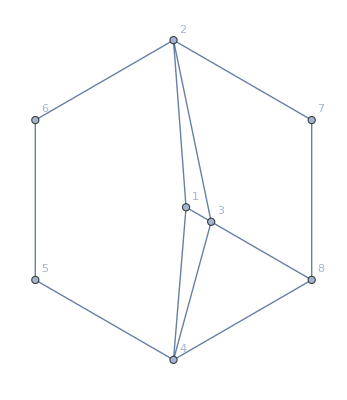

```mathematica
h=EdgeDelete[g,{3<->7,1<->6,1<->5}]
```

```mathematica
solutions2=Select[FindFullFormula[h],SymbolLevel[#]==4&]
```

{v1x28x35x467,v1x28x357x46,v1x258x3x467,v1x258x37x46,v1x258x367x4,v1x258x36x47,v1x24x367x58,v1x24x357x68,v18x2x35x467,v18x2x357x46,v18x25x3x467,v18x25x37x46,v18x25x367x4,v18x25x36x47,v18x24x367x5,v18x24x36x57,v18x24x357x6,v18x24x35x67,v17x28x35x46,v17x258x3x46,v17x258x36x4,v17x24x36x58,v17x24x35x68,v168x2x357x4,v168x2x35x47,v16x28x357x4,v167x28x35x4,v16x28x35x47,v167x258x3x4,v16x258x3x47,v168x25x3x47,v16x258x37x4,v168x25x37x4,v167x24x3x58,v168x24x3x57,v168x24x37x5,v16x24x37x58,v168x24x35x7,v16x24x357x8,v167x24x35x8,v158x2x3x467,v158x2x37x46,v158x2x367x4,v158x2x36x47,v15x28x3x467,v157x28x3x46,v15x28x37x46,v15x28x367x4,v157x28x36x4,v15x28x36x47,v157x24x3x68,v158x24x3x67,v158x24x37x6,v15x24x37x68,v158x24x36x7,v15x24x367x8,v157x24x36x8}

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,PartitionHasPattern[SymbolToSets[#],{{3,7}}]&&!PartitionHasPatternFast[SymbolToSets[#],{{1,6}}]&&PartitionHasPattern[SymbolToSets[#],{{1,5}}]&]], TableSpacing->{0, 0},TableHeadings->{Range[20], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,
(
PartitionHasPattern[SymbolToSets[#],{{2},{3,5},{4,6}}]||
PartitionHasPattern[SymbolToSets[#],{{2,4},{3},{4,5}}]||
PartitionHasPattern[SymbolToSets[#],{{2,5},{3,6},{4}}]||
PartitionHasPattern[SymbolToSets[#],{{2,4},{3,6},{5}}]||
PartitionHasPattern[SymbolToSets[#],{{2,4},{3,5},{6}}]
)&&
PartitionHasPattern[SymbolToSets[#],{{3,7}}]&&
!PartitionHasPattern[SymbolToSets[#],{{1,6}}]&&
PartitionHasPattern[SymbolToSets[#],{{1,5}}]
&]
], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,!PartitionHasPattern[SymbolToSets[#],{{3,7}}]&&PartitionHasPatternFast[SymbolToSets[#],{{1,6}}]&&!PartitionHasPattern[SymbolToSets[#],{{1,5}}]&]], TableSpacing->{0, 0},TableHeadings->{Range[20], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
8 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
9 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
10 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]

## Removing two edges

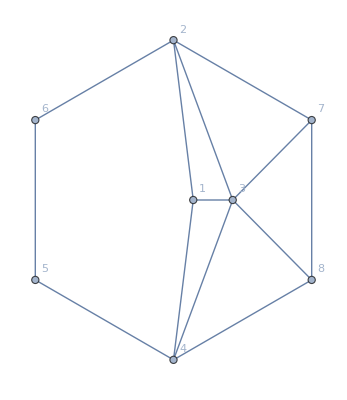

```mathematica
h=EdgeDelete[g,{1<->6,1<->5}]
```

```mathematica
solutions2=Select[FindFullFormula[h],SymbolLevel[#]==4&]
```

{v1x28x35x467,v1x258x3x467,v1x258x36x47,v18x2x35x467,v18x25x3x467,v18x25x36x47,v18x24x36x57,v18x24x35x67,v17x28x35x46,v17x258x3x46,v17x258x36x4,v17x24x36x58,v17x24x35x68,v168x2x35x47,v167x28x35x4,v16x28x35x47,v167x258x3x4,v16x258x3x47,v168x25x3x47,v167x24x3x58,v168x24x3x57,v168x24x35x7,v167x24x35x8,v158x2x3x467,v158x2x36x47,v15x28x3x467,v157x28x3x46,v157x28x36x4,v15x28x36x47,v157x24x3x68,v158x24x3x67,v158x24x36x7,v157x24x36x8}

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,!PartitionHasPatternFast[SymbolToSets[#],{{1,6}}]&&PartitionHasPattern[SymbolToSets[#],{{1,5}}]&]], TableSpacing->{0, 0},TableHeadings->{Range[20], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
8 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
9 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
10 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,!PartitionHasPattern[SymbolToSets[#],{{3,7}}]&&PartitionHasPatternFast[SymbolToSets[#],{{1,6}}]&&!PartitionHasPattern[SymbolToSets[#],{{1,5}}]&]], TableSpacing->{0, 0},TableHeadings->{Range[20], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
8 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
9 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
10 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,solutions2], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
8 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
9 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
10 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
11 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
12 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
13 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
14 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
15 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
16 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
17 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
18 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
19 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
20 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
21 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
22 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
23 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
24 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
25 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
26 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
27 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
28 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
29 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
30 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
31 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
32 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
33 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]

```mathematica
SymbolToNumbers[s_]:=Block[{sets=SymbolToSets[s],result={},colors={Red,Blue,Yellow,Green,Orange },colorpos=1},
Table[
Table[
AppendTo[result,v->colorpos]
,{v,block}
];
colorpos++;
If[colorpos>Length[colors],colorpos=1];
,{block,sets}
];
result
]
```

```mathematica
TableForm[Sort[Map[(Range[8]/.SymbolToNumbers[#])&,solutions]], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | 1 | 2 | 3 | 2 | 3 | 1 | 1 | 4
2 | 1 | 2 | 3 | 2 | 3 | 1 | 3 | 4
3 | 1 | 2 | 3 | 2 | 3 | 1 | 4 | 1
4 | 1 | 2 | 3 | 2 | 3 | 4 | 1 | 4
5 | 1 | 2 | 3 | 2 | 3 | 4 | 3 | 1
6 | 1 | 2 | 3 | 2 | 3 | 4 | 3 | 4
7 | 1 | 2 | 3 | 2 | 3 | 4 | 4 | 1
8 | 1 | 2 | 3 | 2 | 4 | 1 | 1 | 4
9 | 1 | 2 | 3 | 2 | 4 | 1 | 3 | 1
10 | 1 | 2 | 3 | 2 | 4 | 1 | 3 | 4
11 | 1 | 2 | 3 | 2 | 4 | 1 | 4 | 1
12 | 1 | 2 | 3 | 2 | 4 | 3 | 1 | 4
13 | 1 | 2 | 3 | 2 | 4 | 3 | 3 | 1
14 | 1 | 2 | 3 | 2 | 4 | 3 | 3 | 4
15 | 1 | 2 | 3 | 2 | 4 | 3 | 4 | 1
16 | 1 | 2 | 3 | 4 | 2 | 1 | 1 | 2
17 | 1 | 2 | 3 | 4 | 2 | 1 | 3 | 1
18 | 1 | 2 | 3 | 4 | 2 | 1 | 3 | 2
19 | 1 | 2 | 3 | 4 | 2 | 1 | 4 | 1
20 | 1 | 2 | 3 | 4 | 2 | 1 | 4 | 2
21 | 1 | 2 | 3 | 4 | 2 | 3 | 1 | 2
22 | 1 | 2 | 3 | 4 | 2 | 3 | 3 | 1
23 | 1 | 2 | 3 | 4 | 2 | 3 | 3 | 2
24 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 1
25 | 1 | 2 | 3 | 4 | 2 | 3 | 4 | 2
26 | 1 | 2 | 3 | 4 | 2 | 4 | 1 | 2
27 | 1 | 2 | 3 | 4 | 2 | 4 | 3 | 1
28 | 1 | 2 | 3 | 4 | 2 | 4 | 3 | 2
29 | 1 | 2 | 3 | 4 | 2 | 4 | 4 | 1
30 | 1 | 2 | 3 | 4 | 2 | 4 | 4 | 2
31 | 1 | 2 | 3 | 4 | 3 | 1 | 1 | 2
32 | 1 | 2 | 3 | 4 | 3 | 1 | 3 | 1
33 | 1 | 2 | 3 | 4 | 3 | 1 | 3 | 2
34 | 1 | 2 | 3 | 4 | 3 | 1 | 4 | 1
35 | 1 | 2 | 3 | 4 | 3 | 1 | 4 | 2
36 | 1 | 2 | 3 | 4 | 3 | 4 | 1 | 2
37 | 1 | 2 | 3 | 4 | 3 | 4 | 3 | 1
38 | 1 | 2 | 3 | 4 | 3 | 4 | 3 | 2
39 | 1 | 2 | 3 | 4 | 3 | 4 | 4 | 1
40 | 1 | 2 | 3 | 4 | 3 | 4 | 4 | 2

```mathematica
TableForm[Sort[Map[((Range[8])/.SymbolToColoring[#])&,Sort[solutions,SymbolToNumbers[#1]<SymbolToNumbers[#2]&]]], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
8 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
9 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
10 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
11 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
12 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
13 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
14 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
15 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
16 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
17 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
18 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
19 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
20 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
21 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
22 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
23 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
24 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
25 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
26 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
27 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
28 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
29 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
30 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
31 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
32 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
33 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
34 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
35 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
36 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
37 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
38 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
39 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
40 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]